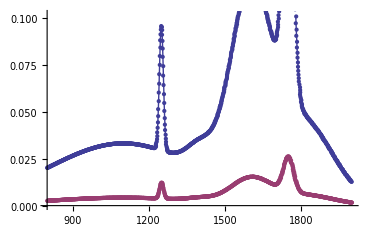

FittedModel[0.127507 ((ⅇ^(-«23» («1»)^2))/(9 √(2 π))+(13 ⅇ^(-«22» «1»))/(36 √(2 π))+ⅇ^(«1»)/(4 √(2 π))+ⅇ^(«1»)/(36 √(«1»))+ⅇ^(-«21» «1»)/(6 √(2 π))+(ⅇ^(-«21» («1»)^2))/(12 √(2 π)))]

| Estimate | Standard Error | t-Statistic | P-Value
scale | 0.127507 | 0.0000623999 | 2043.38 | 8.55027273301×10^-2126
f | 1.00065 | 0.0000186551 | 53639.4 | 2.90426519815×10^-3827

dist->2.80049 H0->69.6071

```mathematica
peaks={1100,1250,1400,1600,1750,1800};
widths={300,8,50,80,20,125};
coeffs={1/12,1/6,1/36,1/4,13/36,1/9};
distance=2.8;(*in Mpc*)
vel=70*distance;(*in km/s*)

factor=Sqrt[(3.00*10^5+vel)/(3.00*10^5-vel)];
coeffs=coeffs/Total[coeffs];

functions[x_]:=Table[coeffs[[i]]*
widths[[i]]*
PDF[NormalDistribution[peaks[[i]],widths[[i]]]][x],
{i,Length[peaks]}];
redfunctions[x_]:=Table[coeffs[[i]]*
widths[[i]]*factor/(distance^2)
PDF[NormalDistribution[peaks[[i]]*factor,widths[[i]]*factor]][x],
{i,Length[peaks]}]

(*Migrate the x to use a random variate with 2400 pts in (800-2000).
Need to fix up the random bit to scale with lambda and signal
*)
pointlist=Table[{x*(1+(2Random[]-1)/1000),Total[functions[x]]*(1+(2*Random[]-1)/1000)},{x,800,2000,1}];
redshifted=Table[{pointlist[[i,1]]*factor,pointlist[[i,2]]/(distance)^2},{i,Length[pointlist]}];

Show[ListPlot[{pointlist,redshifted}],
Plot[{Total[functions[x]],Total[redfunctions[x]]},{x,800,2000}]]

NonlinearModelFit[redshifted,
scale*Total[Table[coeffs[[i]]*widths[[i]]*f*PDF[NormalDistribution[f*peaks[[i]],f*widths[[i]]]][x],{i,Length[coeffs]}]],{scale,f},{x},
MaxIterations->1000,
Method->NMinimize]

%["ParameterTable"]
fit=%%["BestFitParameters"];
d=1/Sqrt[scale]/.fit;
v=(f^2-1)/(f^2+1)*3.00*10^5/.fit;
Print["dist->"<>ToString[d]<>" H0->"<>ToString[v/d]]
```

```mathematica
results={"d/Mpc","v/km/s"};
allData={};
```

```mathematica
AppendTo[results,{d,v}]
AppendTo[allData,redshifted]
```

{{d/Mpc,v/km/s},{2.99982,214.733},{1.00044,66.6299},{3.0015,186.717},{0.8502,67.3117},{1.50077,100.308},{2.60142,186.66},{2.29996,148.403},{1.40009,96.6322},{0.750163,53.4749},{0.29994,20.6236},{0.999523,76.9378},{2.20108,167.841},{0.500324,39.6434},{1.69929,114.704},{2.80049,194.934}}

{{{800.332,0.00223985},{801.684,0.00224911},{803.087,0.00225762},{803.968,0.00226403},«1194»,{1998.45,0.00144797},{2001.3,0.00142794},{2000.18,0.00141052}},«13»,{«1»}}

```mathematica
LinearModelFit[results[[2;;Length[results]]],x,x,IncludeConstantBasis->False]["ParameterConfidenceIntervals",ConfidenceLevel->.90]
```

{{66.9679,71.1999}}